```mathematica
HarmonicOscillator :=DSolve[x''[t]+b x'[t]+k x[t]==0, x[t], t]
HarmonicOscillator
```

{{x[t]→ⅇ^(1/2 (-b-√(b^2-4 k)) t) C[1]+ⅇ^(1/2 (-b+√(b^2-4 k)) t) C[2]}}

```mathematica
expt1 = DSolve[{x''[t]+b x'[t]+k x[t]== 0,x[0]== 1,x'[0]==0},x[t],t]
```

{{x[t]→(-b ⅇ^(1/2 (-b-√(b^2-4 k)) t)+b ⅇ^(1/2 (-b+√(b^2-4 k)) t)+ⅇ^(1/2 (-b-√(b^2-4 k)) t) √(b^2-4 k)+ⅇ^(1/2 (-b+√(b^2-4 k)) t) √(b^2-4 k))/(2 √(b^2-4 k))}}

```mathematica
expt2=(-b ⅇ^(1/2 (-b-√(b^2-4 k)) t)+b ⅇ^(1/2 (-b+√(b^2-4 k)) t)+ⅇ^(1/2 (-b-√(b^2-4 k)) t) √(b^2-4 k)+ⅇ^(1/2 (-b+√(b^2-4 k)) t) √(b^2-4 k))/(2 √(b^2-4 k))/.{b->0.25, k->1}
```

(0.-0.251976 ⅈ) ((-0.25+1.98431 ⅈ) ⅇ^((-0.125-0.992157 ⅈ) t)+(0.25+1.98431 ⅈ) ⅇ^((-0.125+0.992157 ⅈ) t))

```mathematica
expt1plot[b0_]:=Plot[x[t]/.expt1/.{b->b0,k->1},{t,0,40}, PlotRange->{{0,40},{-1,1}}, PlotLabel->If[b0<2, "Underdamped", "Overdamped"], AxesLabel->{"t", "x[t]"}, PlotStyle->{Thick, Red}]
```

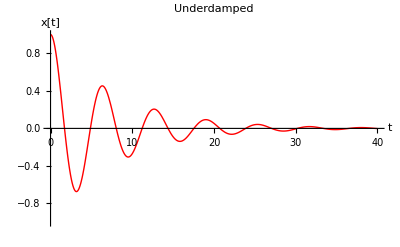

```mathematica
plot1 = expt1plot[0.25]
```

```mathematica
y=Re[Table[expt2,{t,0, 40,1}]]
```

{1.,0.575709,-0.223098,-0.663708,-0.466895,0.0662262,0.427543,0.361108,0.0155891,-0.266184,-0.269075,-0.05242,0.158957,0.194258,0.0637116,-0.089791,-0.136289,-0.0616239,0.0466598,0.0930311,0.0534595,-0.0208509,-0.0617606,-0.0433757,0.00623082,0.0397953,0.0335599,0.001401,-0.0247841,-0.025014,-0.00484283,0.0148064,0.0180634,0.00590451,-0.00836849,-0.0126761,-0.00571823,0.00435265,0.00865476,0.00496415,-0.00194869}

```mathematica
noise= RandomReal[0.005]
```

0.00297966

```mathematica
list= Table[If[y[[i]]>0, y[[i]]+noise, y[[i]]-noise],{i,1,Length[y]}]
```

{1.00298,0.578689,-0.226078,-0.666687,-0.469874,0.0692059,0.430522,0.364088,0.0185687,-0.269164,-0.272055,-0.0553997,0.161937,0.197238,0.0666912,-0.0927706,-0.139269,-0.0646036,0.0496394,0.0960107,0.0564392,-0.0238305,-0.0647403,-0.0463554,0.00921047,0.042775,0.0365395,0.00438066,-0.0277638,-0.0279936,-0.00782248,0.017786,0.0210431,0.00888417,-0.0113481,-0.0156558,-0.00869789,0.00733231,0.0116344,0.00794381,-0.00492834}

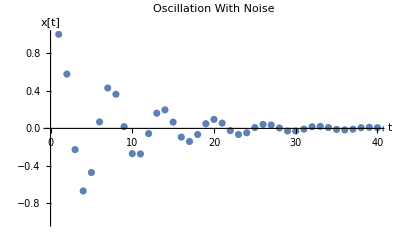

```mathematica
plot2 = ListPlot[list, PlotRange->{{0,40},{-1,1}},AxesLabel->{"t","x[t]"} , PlotLabel->"Oscillation With Noise"]
```

```mathematica
least = Fit[list, expt2,t]
```

(0.-0.188171 ⅈ) ((-0.25+1.98431 ⅈ) ⅇ^((-0.125-0.992157 ⅈ) t)+(0.25+1.98431 ⅈ) ⅇ^((-0.125+0.992157 ⅈ) t))

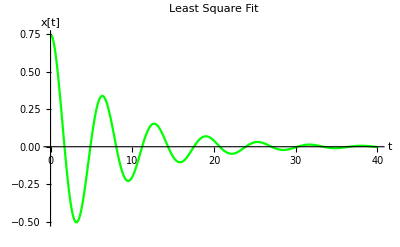

```mathematica
plot3 = Plot[least, {t,0,40}, PlotRange->All, PlotStyle->Green,AxesLabel->{"t","x[t]"} , PlotLabel->"Least Square Fit"]
```

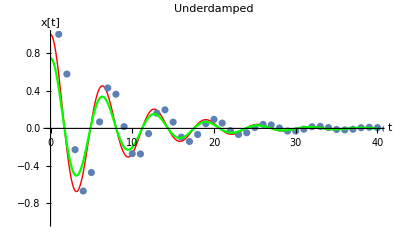

```mathematica
Show[plot1,plot2,plot3]
```

```mathematica
velocity1 = D[expt2, t]
```

(0.-0.251976 ⅈ) ((2.+0. ⅈ) ⅇ^((-0.125-0.992157 ⅈ) t)-(2.+0. ⅈ) ⅇ^((-0.125+0.992157 ⅈ) t))

```mathematica
velocity = Re[Table[velocity1, {t,0,40,0.1}]]
```

{0.,-0.0985958,-0.193784,-0.284711,-0.370582,-0.450677,-0.524347,-0.591024,-0.650222,-0.701543,-0.744674,-0.779391,-0.805561,-0.823135,-0.832153,-0.832737,-0.825089,-0.809488,-0.786284,-0.755894,-0.718796,-0.67552,-0.626648,-0.572798,-0.514625,-0.452811,-0.388055,-0.321068,-0.252567,-0.183264,-0.113865,-0.0450553,0.0225,0.0881653,0.151339,0.21146,0.26801,0.320519,0.368569,0.411795,0.449891,0.482606,0.509752,0.531197,0.546871,0.556762,0.560914,0.559429,0.55246,0.540212,0.522935,0.500925,0.474515,0.444074,0.410004,0.372728,0.332695,0.290368,0.24622,0.200733,0.154387,0.107663,0.06103,0.014946,-0.0301476,-0.0738304,-0.115706,-0.155406,-0.192592,-0.22696,-0.25824,-0.286199,-0.310643,-0.331419,-0.348411,-0.361546,-0.370789,-0.376144,-0.377656,-0.375404,-0.369503,-0.360101,-0.347378,-0.331542,-0.312825,-0.291483,-0.267792,-0.242043,-0.214541,-0.185602,-0.155545,-0.124696,-0.0933776,-0.0619113,-0.030611,0.000218583,0.0302848,0.0593099,0.0870331,0.113213,0.137629,0.160085,0.180406,0.198445,0.214081,0.227218,0.237789,0.245752,0.251093,0.253825,0.253985,0.251635,0.246859,0.239766,0.230481,0.219152,0.20594,0.191021,0.174586,0.156835,0.137973,0.118216,0.0977806,0.0768845,0.0557456,0.0345786,0.0135931,-0.00700854,-0.0270323,-0.046295,-0.0646252,-0.0818651,-0.0978716,-0.112517,-0.125691,-0.137299,-0.147265,-0.155533,-0.162061,-0.166829,-0.169833,-0.171087,-0.170622,-0.168485,-0.164738,-0.159457,-0.152734,-0.144669,-0.135376,-0.124977,-0.113601,-0.101385,-0.0884704,-0.0750014,-0.0611249,-0.0469878,-0.0327361,-0.0185133,-0.00445887,0.00929251,0.0226127,0.0353808,0.0474846,0.0588209,0.069297,0.0788305,0.0873508,0.0947988,0.101127,0.106302,0.1103,0.11311,0.114735,0.115188,0.114493,0.112685,0.10981,0.105923,0.101086,0.0953708,0.0888559,0.081625,0.0737671,0.0653754,0.0565458,0.0473761,0.0379654,0.0284124,0.0188149,0.00926865,-0.000133328,-0.00930186,-0.0181522,-0.026605,-0.0345864,-0.0420296,-0.0488742,-0.0550676,-0.0605646,-0.0653283,-0.0693297,-0.0725482,-0.0749713,-0.0765948,-0.0774224,-0.0774656,-0.0767433,-0.0752815,-0.073113,-0.0702765,-0.0668166,-0.0627828,-0.0582291,-0.0532132,-0.047796,-0.042041,-0.0360132,-0.0297788,-0.0234045,-0.0169567,-0.0105007,-0.00410049,0.00218215,0.00828813,0.0141616,0.0197503,0.0250061,0.0298854,0.0343493,0.038364,0.0419011,0.0449373,0.0474552,0.0494426,0.050893,0.0518055,0.0521842,0.0520386,0.0513831,0.0502367,0.0486229,0.0465692,0.0441066,0.0412696,0.0380954,0.0346237,0.030896,0.0269555,0.0228462,0.018613,0.0143007,0.00995367,0.00561577,0.00132956,-0.00286394,-0.00692564,-0.0108187,-0.0145089,-0.0179648,-0.0211582,-0.0240639,-0.0266603,-0.0289296,-0.0308575,-0.0324332,-0.0336499,-0.0345046,-0.0349977,-0.0351332,-0.0349188,-0.034365,-0.0334858,-0.0322979,-0.0308206,-0.0290757,-0.0270869,-0.0248799,-0.0224819,-0.0199213,-0.0172273,-0.0144299,-0.0115591,-0.0086451,-0.00571777,-0.00280629,0.0000609941,0.00285688,0.00555555,0.00813276,0.0105661,0.0128351,0.0149214,0.016809,0.018484,0.0199354,0.0211542,0.0221341,0.0228714,0.0233649,0.0236156,0.023627,0.0234051,0.0229576,0.0222947,0.0214281,0.0203715,0.01914,0.01775,0.0162191,0.014566,0.01281,0.0109709,0.00906903,0.00712457,0.00515783,0.00318874,0.00123681,-0.000679137,-0.00254108,-0.00433197,-0.0060359,-0.00763819,-0.00912556,-0.0104861,-0.0117097,-0.0127874,-0.0137124,-0.0144792,-0.0150842,-0.0155255,-0.0158026,-0.0159169,-0.0158714,-0.0156704,-0.0153197,-0.0148265,-0.0141991,-0.0134472,-0.0125811,-0.0116122,-0.0105527,-0.00941519,-0.00821287,-0.0069592,-0.00566781,-0.00435237,-0.00302646,-0.00170343,-0.000396248,0.000882567,0.0021211,0.00330812,0.00443319,0.00548673,0.00646013,0.00734574,0.008137,0.00882842,0.00941566,0.00989549,0.0102658,0.0105257,0.0106753,0.0107159,0.0106497,0.0104801,0.0102112,0.00984826,0.00939706,0.00886428,0.00825717,0.00758358,0.00685178,0.00607044,0.00524849,0.00439504,0.0035193,0.00263045,0.00173758,0.000849621,-0.0000248029,-0.000877392,-0.00170027,-0.00248606,-0.00322791,-0.00391959,-0.00455552,-0.0051308,-0.00564124,-0.00608341,-0.00645463,-0.006753,-0.00697736,-0.00712733,-0.00720327,-0.00720625,-0.00713805,-0.00700109,-0.00679843,-0.00653369,-0.00621102}

```mathematica
position1 = expt2
```

(0.-0.251976 ⅈ) ((-0.25+1.98431 ⅈ) ⅇ^((-0.125-0.992157 ⅈ) t)+(0.25+1.98431 ⅈ) ⅇ^((-0.125+0.992157 ⅈ) t))

```mathematica
position = Re[Table[position1, {t,0,40,0.1}]]
```

{1.,0.995046,0.980394,0.956431,0.923621,0.882507,0.8337,0.777871,0.715744,0.648089,0.575709,0.499435,0.420116,0.338609,0.255774,0.17246,0.0895012,0.00770746,-0.0721428,-0.14931,-0.223098,-0.292863,-0.358015,-0.418027,-0.472431,-0.52083,-0.562895,-0.598367,-0.627058,-0.648853,-0.663708,-0.671646,-0.672761,-0.667209,-0.655211,-0.637043,-0.613038,-0.583576,-0.549083,-0.510023,-0.466895,-0.420224,-0.370559,-0.318464,-0.264512,-0.209283,-0.153351,-0.0972878,-0.0416484,0.0130282,0.0662262,0.117457,0.166264,0.212226,0.254958,0.29412,0.329412,0.360582,0.387425,0.409782,0.427543,0.440647,0.449079,0.452871,0.452101,0.446888,0.437395,0.42382,0.406398,0.385395,0.361108,0.333858,0.303986,0.271852,0.237828,0.202298,0.165649,0.12827,0.0905482,0.0528642,0.0155891,-0.0209196,-0.0563204,-0.0902915,-0.122533,-0.152769,-0.180751,-0.206259,-0.229101,-0.249119,-0.266184,-0.280202,-0.291108,-0.298872,-0.303496,-0.30501,-0.303477,-0.298988,-0.291659,-0.281633,-0.269075,-0.254172,-0.237129,-0.218167,-0.19752,-0.175434,-0.152162,-0.127963,-0.103099,-0.0778317,-0.05242,-0.0271184,-0.00217391,0.0221762,0.0457062,0.0682042,0.0894738,0.109335,0.127627,0.144209,0.158957,0.171773,0.182578,0.191314,0.197947,0.202462,0.204869,0.205194,0.203486,0.199813,0.194258,0.186924,0.177926,0.167395,0.155472,0.142309,0.128067,0.112913,0.0970186,0.0805594,0.0637116,0.0466511,0.0295515,0.0125824,-0.00409181,-0.020314,-0.0359352,-0.050816,-0.0648281,-0.0778545,-0.089791,-0.100547,-0.110045,-0.118222,-0.125031,-0.130439,-0.134425,-0.136987,-0.138133,-0.137889,-0.136289,-0.133385,-0.129235,-0.123913,-0.1175,-0.110085,-0.101767,-0.0926508,-0.082845,-0.0724639,-0.0616239,-0.0504435,-0.0390414,-0.0275356,-0.0160421,-0.00467406,0.0064594,0.0172542,0.0276123,0.0374421,0.0466598,0.0551894,0.0629639,0.069925,0.0760243,0.0812229,0.0854915,0.0888112,0.0911725,0.0925759,0.0930311,0.092557,0.0911813,0.0889398,0.085876,0.0820405,0.0774901,0.0722873,0.0664998,0.0601989,0.0534595,0.046359,0.0389764,0.0313914,0.023684,0.0159331,0.00821638,0.000609105,-0.00681636,-0.0139912,-0.0208509,-0.0273354,-0.0333901,-0.0389658,-0.0440194,-0.0485138,-0.0524185,-0.0557095,-0.0583696,-0.060388,-0.0617606,-0.06249,-0.0625846,-0.0620594,-0.0609348,-0.0592366,-0.0569958,-0.0542479,-0.0510326,-0.0473931,-0.0433757,-0.0390296,-0.0344056,-0.0295562,-0.0245349,-0.0193955,-0.0141916,-0.0089762,-0.00380094,0.00128405,0.00623082,0.010994,0.015531,0.0198028,0.0237737,0.027412,0.0306899,0.0335841,0.0360754,0.0381492,0.0397953,0.0410082,0.0417864,0.042133,0.0420554,0.0415647,0.0406759,0.0394077,0.0377819,0.0358235,0.0335599,0.031021,0.0282387,0.0252465,0.022079,0.0187718,0.0153611,0.0118829,0.00837344,0.00486796,0.001401,-0.00199418,-0.00528587,-0.00844411,-0.0114411,-0.0142511,-0.0168512,-0.0192207,-0.0213421,-0.0232005,-0.0247841,-0.0260841,-0.0270945,-0.0278126,-0.0282386,-0.0283754,-0.0282288,-0.0278072,-0.0271217,-0.0261855,-0.025014,-0.0236246,-0.0220363,-0.0202699,-0.018347,-0.0162905,-0.0141241,-0.0118718,-0.00955796,-0.00720693,-0.00484283,-0.0024893,-0.000169328,0.00209504,0.00428282,0.00637433,0.0083513,0.010197,0.0118966,0.0134368,0.0148064,0.015996,0.0169985,0.0178084,0.0184226,0.0188399,0.019061,0.0190885,0.0189269,0.0185826,0.0180634,0.0173788,0.0165396,0.0155579,0.014447,0.0132209,0.0118946,0.0104837,0.00900413,0.00747228,0.00590451,0.00431719,0.00272645,0.00114809,-0.000402629,-0.00191109,-0.00336345,-0.00474676,-0.00604908,-0.00725955,-0.00836849,-0.00936748,-0.0102494,-0.0110083,-0.01164,-0.0121411,-0.0125101,-0.0127465,-0.0128513,-0.0128267,-0.0126761,-0.0124042,-0.0120166,-0.0115199,-0.0109219,-0.0102308,-0.00945589,-0.00860677,-0.00769368,-0.00672722,-0.00571823,-0.00467773,-0.00361677,-0.0025463,-0.00147715,-0.000419808,0.000615566,0.0016193,0.00258228,0.00349599,0.00435265,0.00514521,0.00586743,0.00651392,0.00708016,0.00756256,0.00795843,0.00826599,0.00848438,0.00861367,0.00865476,0.00860944,0.00848027,0.00827062,0.00798453,0.00762671,0.00720247,0.00671763,0.00617847,0.00559166,0.00496415,0.00430316,0.00361602,0.00291017,0.00219302,0.00147195,0.000754147,0.0000466286,-0.000643881,-0.00131099,-0.00194869}

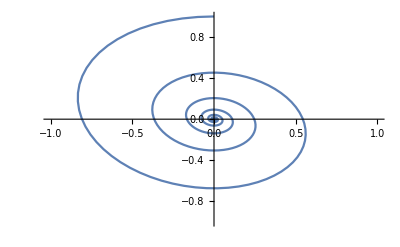

```mathematica
ListPlot[Thread[{velocity,position}],Joined->True, PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
forcedUd=DSolve[{x''[t]+1* x'[t]+3*x[t]== 3*Cos[2*t],x[0]== 8,x'[0]==0},x[t],t]
```

{{x[t]→1/(22 (-7+2 √11) (7+2 √11))ⅇ^(-t/2) (-946 Cos[(√11 t)/2]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-38 √11 Sin[(√11 t)/2]-66 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+66 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2])}}

```mathematica
x=1/(22 (-7+2 √11) (7+2 √11))ⅇ^(-t/2) (-946 Cos[(√11 t)/2]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-38 √11 Sin[(√11 t)/2]-66 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+66 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2])
```

1/(22 (-7+2 √11) (7+2 √11))ⅇ^(-t/2) (-946 Cos[(√11 t)/2]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-38 √11 Sin[(√11 t)/2]-66 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+66 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2])

```mathematica
v= D[x, t]
```

-1/(44 (-7+2 √11) (7+2 √11))ⅇ^(-t/2) (-946 Cos[(√11 t)/2]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]+33 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-38 √11 Sin[(√11 t)/2]-66 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+66 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+33 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-18 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-66 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2]-21 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2])+1/(22 (-7+2 √11) (7+2 √11))ⅇ^(-t/2) (-209 Cos[(√11 t)/2]-99 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]-24 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (-4+√11) t]-99 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]+24 √11 ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-33 (4+√11) ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]+21/2 √11 (4+√11) ⅇ^(t/2) Cos[(√11 t)/2] Cos[1/2 (4+√11) t]-66 (2-(√11)/2) ⅇ^(t/2) Cos[(√11 t)/2] Cos[2 t-(√11 t)/2]-21 √11 (2-(√11)/2) ⅇ^(t/2) Cos[(√11 t)/2] Cos[2 t-(√11 t)/2]+473 √11 Sin[(√11 t)/2]-132 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]-27 √11 ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+33/2 (-4+√11) ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+9 √11 (-4+√11) ⅇ^(t/2) Cos[1/2 (-4+√11) t] Sin[(√11 t)/2]+132 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]-27 √11 ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]+33/2 (4+√11) ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]-9 √11 (4+√11) ⅇ^(t/2) Cos[1/2 (4+√11) t] Sin[(√11 t)/2]+99 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (-4+√11) t]+33/2 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (-4+√11) t]-33/2 (-4+√11) ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (-4+√11) t]-9 √11 (-4+√11) ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (-4+√11) t]+33/2 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+9 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+33 (-4+√11) ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]+21/2 √11 (-4+√11) ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (-4+√11) t]-132 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+27 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]-33/2 (4+√11) ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]+9 √11 (4+√11) ⅇ^(t/2) Cos[(√11 t)/2] Sin[1/2 (4+√11) t]-99 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]+24 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-33 (4+√11) ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]+21/2 √11 (4+√11) ⅇ^(t/2) Sin[(√11 t)/2] Sin[1/2 (4+√11) t]-33 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2]-21/2 √11 ⅇ^(t/2) Cos[(√11 t)/2] Sin[2 t-(√11 t)/2]+231/2 ⅇ^(t/2) Sin[(√11 t)/2] Sin[2 t-(√11 t)/2]+33 √11 ⅇ^(t/2) Sin[(√11 t)/2] Sin[2 t-(√11 t)/2])

```mathematica
positionf= Re[Table[x,{t,0,40,0.1}]]
```

{8.,7.89862,7.60976,7.1578,6.56842,5.86781,5.08207,4.23662,3.35575,2.46227,1.5772,0.719585,-0.0936487,-0.847787,-1.53036,-2.13116,-2.6422,-3.05769,-3.374,-3.58956,-3.7048,-3.72209,-3.64561,-3.48127,-3.23656,-2.92045,-2.54315,-2.11599,-1.65118,-1.16153,-0.660249,-0.160602,0.324359,0.782117,1.201,1.57046,1.88142,2.12643,2.29997,2.39859,2.421,2.36816,2.24324,2.05154,1.80037,1.49878,1.15732,0.787729,0.402498,0.0145241,-0.363333,-0.718674,-1.03997,-1.31697,-1.54099,-1.70528,-1.80519,-1.83839,-1.80486,-1.70696,-1.54928,-1.33851,-1.08317,-0.793277,-0.480019,-0.155301,0.168675,0.479861,0.766813,1.0191,1.22771,1.38533,1.48668,1.52862,1.51033,1.43326,1.30112,1.11968,0.896561,0.640918,0.363093,0.0742,-0.214308,-0.49108,-0.745312,-0.967159,-1.14812,-1.28134,-1.36192,-1.38705,-1.3561,-1.27071,-1.13462,-0.953592,-0.735119,-0.488152,-0.222731,0.0504165,0.3203,0.576105,0.807623,1.00565,1.16235,1.27157,1.32906,1.33267,1.28241,1.18041,1.03092,0.840039,0.615525,0.366467,0.102918,-0.164507,-0.425053,-0.668259,-0.884374,-1.06474,-1.20216,-1.29113,-1.32813,-1.31171,-1.24255,-1.12346,-0.959233,-0.756478,-0.523336,-0.269162,-0.00414767,0.261084,0.515906,0.750111,0.954322,1.12036,1.24158,1.31313,1.33213,1.29783,1.2116,1.07686,0.899011,0.68515,0.443822,0.184667,-0.0819598,-0.345407,-0.595148,-0.821203,-1.01454,-1.16743,-1.27375,-1.32926,-1.33173,-1.28104,-1.17922,-1.03031,-0.840245,-0.616608,-0.368314,-0.105265,0.162046,0.422956,0.667055,0.884603,1.06692,1.20672,1.29843,1.33839,1.32498,1.25875,1.14232,0.980325,0.779227,0.547038,0.29301,0.0272722,-0.239583,-0.496916,-0.734466,-0.942761,-1.11349,-1.23985,-1.3168,-1.34126,-1.31227,-1.23096,-1.10058,-0.926317,-0.715126,-0.47542,-0.216753,0.0505648,0.315877,0.568608,0.798681,0.996925,1.15544,1.26789,1.32982,1.33873,1.29428,1.19824,1.05443,0.868591,0.648125,0.401821,0.139497,-0.128389,-0.391159,-0.638338,-0.860071,-1.04752,-1.19321,-1.29134,-1.33799,-1.3313,-1.27155,-1.1611,-1.00437,-0.807596,-0.578632,-0.326601,-0.0615507,0.205952,0.465245,0.705989,0.918588,1.09457,1.22691,1.31034,1.34154,1.31925,1.24437,1.11988,0.950751,0.743718,0.507036,0.250142,-0.0167237,-0.282922,-0.53784,-0.771315,-0.97404,-1.13793,-1.25646,-1.3249,-1.34052,-1.30269,-1.21293,-1.07482,-0.893858,-0.677261,-0.433665,-0.172781,0.0949916,0.358976,0.608649,0.834056,1.02621,1.17746,1.28176,1.33496,1.33494,1.2817,1.17737,1.02609,0.833914,0.608489,0.358805,0.0948164,-0.172952,-0.433824,-0.677401,-0.893973,-1.0749,-1.21298,-1.3027,-1.34049,-1.32483,-1.25636,-1.1378,-0.973878,-0.771132,-0.537644,-0.282722,-0.016528,0.250324,0.507197,0.743849,0.950846,1.11994,1.24438,1.31921,1.34145,1.31021,1.22673,1.09435,0.918345,0.705725,0.464969,0.205677,-0.0618147,-0.326842,-0.57884,-0.80776,-1.00448,-1.16115,-1.27153,-1.33122,-1.33784,-1.29112,-1.19293,-1.04718,-0.859683,-0.637913,-0.390711,-0.127933,0.139945,0.402244,0.648507,0.868916,1.05468,1.19841,1.29435,1.33869,1.32967,1.26763,1.15506,0.996436,0.79809,0.567927,0.315122,0.0497545,-0.217597,-0.476273,-0.715962,-0.927108,-1.10129,-1.23157,-1.31275,-1.3416,-1.31696,-1.23982,-1.11325,-0.942294,-0.733776,-0.496004,-0.238459,0.0285937,0.294506,0.548677,0.780975,0.982137,1.14414,1.26054,1.32668,1.33993,1.29976,1.20777,1.06764,0.884938,0.666959,0.42239,0.160982,-0.106844,-0.370411,-0.61921,-0.843324,-1.03382,-1.18309,-1.28521,-1.33608,-1.33369,-1.27813,-1.17161,-1.01839,-0.824564,-0.597867,-0.347335,-0.0829561,0.18473,0.445052,0.687631,0.902797,1.08197,1.21801,1.30549,1.34092,1.3229,1.25214,1.13146,0.965666,0.761378,0.526737,0.271096,0.00464735,-0.261987,-0.518176,-0.753707,-0.959191,-1.12643}

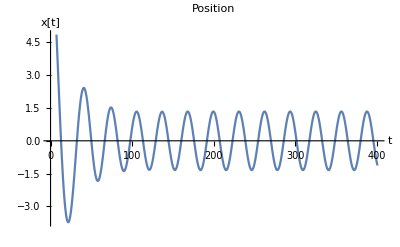

```mathematica
ListPlot[positionf, Joined->True, AxesLabel->{"t","x[t]"}, PlotLabel->"Position"]
```

```mathematica
velocityf = Re[Table[v,{t,0,40,0.1}]]
```

{0.,-1.99038,-3.74605,-5.25015,-6.49374,-7.47484,-8.19754,-8.67096,-8.90835,-8.9262,-8.74342,-8.38062,-7.85952,-7.20247,-6.43201,-5.57064,-4.64051,-3.66334,-2.66023,-1.65163,-0.657162,0.304404,1.21532,2.05898,2.82015,3.48511,4.04194,4.48079,4.79408,4.9768,5.02669,4.94445,4.73386,4.40179,3.95819,3.41596,2.79068,2.10032,1.3648,0.60543,-0.155603,-0.895929,-1.59366,-2.22807,-2.78028,-3.2339,-3.57556,-3.79544,-3.88763,-3.85034,-3.68606,-3.40149,-3.00734,-2.518,-1.95111,-1.3269,-0.667546,0.00363974,0.662998,1.28738,1.85499,2.34613,2.74397,3.03512,3.21012,3.26382,3.19553,3.00905,2.71254,2.31817,1.84172,1.30192,0.719763,0.117718,-0.481138,-1.05399,-1.57915,-2.0369,-2.4102,-2.68535,-2.85254,-2.90616,-2.84501,-2.67236,-2.3958,-2.02691,-1.5808,-1.07553,-0.531372,0.0299624,0.586205,1.11539,1.59671,2.01133,2.34315,2.57939,2.71109,2.73347,2.6461,2.45292,2.16202,1.78538,1.33832,0.838936,0.30735,-0.235089,-0.766655,-1.26611,-1.71353,-2.09113,-2.38394,-2.5804,-2.67282,-2.65767,-2.53574,-2.31207,-1.99575,-1.59958,-1.13952,-0.634071,-0.103523,0.430851,0.947642,1.42617,1.84729,2.19419,2.453,2.61343,2.66908,2.61777,2.46159,2.20683,1.8637,1.44595,0.970314,0.455811,-0.0769707,-0.606727,-1.11228,-1.57341,-1.9717,-2.29122,-2.51921,-2.64655,-2.66816,-2.58316,-2.39495,-2.11103,-1.74274,-1.30478,-0.814624,-0.291845,0.242692,0.767648,1.26207,1.70621,2.08235,2.37547,2.57385,2.66957,2.65881,2.54197,2.32371,2.01272,1.6214,1.16535,0.662752,0.133652,-0.400852,-0.919441,-1.40143,-1.8276,-2.18094,-2.44737,-2.61623,-2.68081,-2.6385,-2.49099,-2.24416,-1.90783,-1.49542,-1.02335,-0.510458,0.0228236,0.55523,1.06554,1.53339,1.94015,2.26958,2.50855,2.64754,2.68099,2.60756,2.43019,2.15593,1.79572,1.36392,0.877737,0.356549,-0.178864,-0.707159,-1.20727,-1.65927,-2.04514,-2.34948,-2.56017,-2.6688,-2.67105,-2.56682,-2.36026,-2.05962,-1.67687,-1.22726,-0.728736,-0.201154,0.334449,0.856721,1.34484,1.77935,2.14293,2.42108,2.60272,2.6806,2.65162,2.51693,2.2819,1.95591,1.55194,1.0861,0.576967,0.0448327,-0.489088,-1.00351,-1.47793,-1.89342,-2.23343,-2.48441,-2.63634,-2.68317,-2.62303,-2.45832,-2.19561,-1.84537,-1.42156,-0.941082,-0.423085,0.111778,0.642183,1.14699,1.60606,2.00111,2.31638,2.5393,2.66099,2.67659,2.58549,2.39131,2.1018,1.7285,1.28629,0.792797,0.267701,-0.268066,-0.793147,-1.28661,-1.72877,-2.10202,-2.39146,-2.58556,-2.67659,-2.66091,-2.53914,-2.31615,-2.00082,-1.60573,-1.14662,-0.641796,-0.111388,0.423461,0.941427,1.42186,1.84561,2.19578,2.45841,2.62303,2.68308,2.63616,2.48415,2.2331,1.89303,1.47749,1.00304,0.488606,-0.0453074,-0.577414,-1.0865,-1.55227,-1.95616,-2.28206,-2.51698,-2.65156,-2.68043,-2.60244,-2.4207,-2.14245,-1.77879,-1.34421,-0.856046,-0.333753,0.201846,0.729398,1.22787,1.67739,2.06004,2.36056,2.56698,2.67105,2.66864,2.55984,2.34899,2.04449,1.65848,1.20635,0.706135,0.177764,-0.357694,-0.878892,-1.36505,-1.79679,-2.1569,-2.43101,-2.60822,-2.68143,-2.64775,-2.50852,-2.26927,-1.93956,-1.53252,-1.06439,-0.553817,-0.02117,0.512321,1.02539,1.49758,1.91006,2.24639,2.49317,2.64056,2.68267,2.61784,2.44863,2.18181,1.82801,1.40133,0.918786,0.399611,-0.135496,-0.6652,-1.16839,-1.62499,-2.01681,-2.32823,-2.54683,-2.6639,-2.67476,-2.57899,-2.3804,-2.08692,-1.71023,-1.26537,-0.770054,-0.244042,0.291699,0.815811,1.3074,1.74687,2.11669,2.40213,2.5918,2.67815,2.65772,2.53135,2.30405,1.9849,1.58662,1.12508,0.618695,0.0876408,-0.446908,-0.963639,-1.44195,-1.86278,-2.20935,-2.46783,-2.62793,-2.68327,-2.63163,-2.47507,-2.21984,-1.87612,-1.4576}

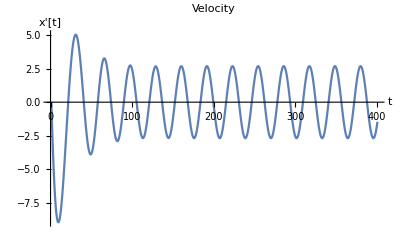

```mathematica
ListPlot[velocityf, Joined->True,AxesLabel->{"t","x'[t]"}, PlotLabel->"Velocity"]
```

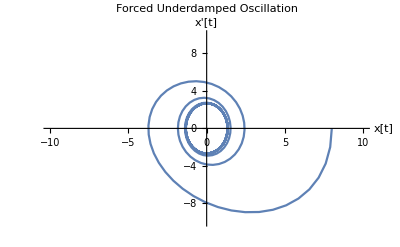

```mathematica
ListPlot[Thread[{positionf,velocityf}],Joined->True, PlotRange->{{-10,10},{-10,10}}, AxesLabel->{"x[t]","x'[t]"}, PlotLabel->"Forced Underdamped Oscillation"]
```